This notebook depends on variables in linear_kstein_slope.nb and fssd_slope.nb. Just run them in the same session to get variables loaded here.

## Case 1: variance is 1, mean shift problem

```mathematica
f$slope$fssd[v,Subscript[μ, q],1,Subscript[σ, k]^2]
```

(ⅇ^(-(v-μ_q)^2/(1+σ_k^2)+v^2/(2+σ_k^2)) μ_q^2 (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/((1+σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
f$slope$fssd$sq1[v,Subscript[μ, q],Subscript[σ, k]^2]
```

(ⅇ^(-(v-μ_q)^2/(1+σ_k^2)+v^2/(2+σ_k^2)) μ_q^2 (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/((1+σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],Subscript[σ, k]^2]
```

(ⅇ^(μ_q^2/(2+σ_k^2)) μ_q^2 (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/((1+σ_k^2) (2+(5+μ_q^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
f$slope$fssd$sq1[2 Subscript[μ, q],Subscript[μ, q],1]
```

(9 √3 ⅇ^((5 μ_q^2)/6) μ_q^2)/(2 (12+4 μ_q^2))

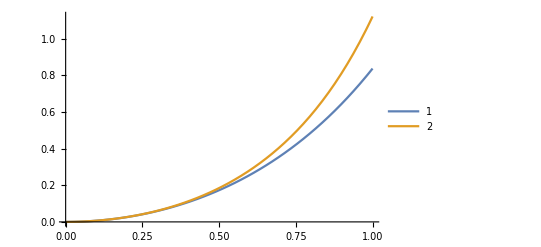

```mathematica
Plot[{f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],1],
f$slope$fssd$sq1[Subscript[μ, q]*2,Subscript[μ, q],1]},{Subscript[μ, q],0,1},PlotLegends->Automatic]
```

```mathematica
Assuming[Subscript[σ, k]>0,Reduce[D[f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],Subscript[σ, k]^2], Subscript[σ, k]]>0,Reals]]
```

μ_q≠0&&(σ_k<Root[-12-36 #1^2+#1^10 μ_q^2+#1^8 (-3+3 μ_q^2)+#1^4 (-39+2 μ_q^2+μ_q^4)+#1^6 (-18+3 μ_q^2+μ_q^4)&,1]||0<σ_k<Root[-12-36 #1^2+#1^10 μ_q^2+#1^8 (-3+3 μ_q^2)+#1^4 (-39+2 μ_q^2+μ_q^4)+#1^6 (-18+3 μ_q^2+μ_q^4)&,2])

```mathematica
Plot3D[f$slope$fssd$sq1[Subscript[μ, q],Subscript[μ, q],Subscript[σ, k]^2],{Subscript[μ, q],0,4},{Subscript[σ, k],0.01,4},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
slope$lkstein$sq1
```

((κ^2)^(5/2) (4+κ^2)^(5/2) μ_q^4)/(2 (2+κ^2) (12+20 κ^2+21 κ^4+8 κ^6+κ^8))

```mathematica
D[(slope$lkstein$sq1), κ]//Simplify
```

(2 κ^3 √(κ^2) (4+κ^2)^(3/2) (120+216 κ^2+166 κ^4+56 κ^6+7 κ^8) μ_q^4)/((2+κ^2)^2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8)^2)

```mathematica
diffs=D[(slope$lkstein$sq1/.{κ->Sqrt[s]}), s]//Simplify
```

(s^(3/2) (4+s)^(3/2) (120+216 s+166 s^2+56 s^3+7 s^4) μ_q^4)/((2+s)^2 (12+20 s+21 s^2+8 s^3+s^4)^2)

```mathematica
diffs/.{s->κ^2}
```

((κ^2)^(3/2) (4+κ^2)^(3/2) (120+216 κ^2+166 κ^4+56 κ^6+7 κ^8) μ_q^4)/((2+κ^2)^2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8)^2)

```mathematica
eff$sq1=Simplify[f$slope$fssd[v,Subscript[μ, q],1,Subscript[σ, k]^2]/f$slope$lkstein$sq1[Subscript[μ, q],κ^2]]
```

(2 ⅇ^(-(v-μ_q)^2/(1+σ_k^2)+v^2/(2+σ_k^2)) (2+κ^2) (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/((κ^2)^(5/2) (4+κ^2)^(5/2) μ_q^2 (1+σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
eff$sq1/.{Subscript[σ, k]->1,v->2 Subscript[μ, q]}
```

(9 √3 ⅇ^((5 μ_q^2)/6) (2+κ^2) (12+20 κ^2+21 κ^4+8 κ^6+κ^8))/((κ^2)^(5/2) (4+κ^2)^(5/2) μ_q^2 (12+4 μ_q^2))

```mathematica
f$slope$lkstein$sq1[Subscript[μ, q],κ^2]
```

((κ^2)^(5/2) (4+κ^2)^(5/2) μ_q^4)/(2 (2+κ^2) (12+20 κ^2+21 κ^4+8 κ^6+κ^8))

```mathematica
Limit[f$slope$lkstein$sq1[Subscript[μ, q],κ^2],κ->∞]
```

μ_q^4/2

```mathematica
Plot3D[f$slope$lkstein$sq1[mq1,ka1^2],{mq1,0,3},{ka1,0.01,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
f$eff$sq1$minmax[v1_,mq1_,sk1_]:=f$slope$fssd$sq1[v1,mq1,sk1]/Limit[f$slope$lkstein$sq1[mq1,κ],κ->∞]
```

```mathematica
f$eff$sq1$minmax[v,Subscript[μ, q],Subscript[σ, k]^2]
```

(2 ⅇ^(-(v-μ_q)^2/(1+σ_k^2)+v^2/(2+σ_k^2)) (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/(μ_q^2 (1+σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
f$eff$sq1$minmax[2 Subscript[μ, q],Subscript[μ, q],1]
```

(9 √3 ⅇ^((5 μ_q^2)/6))/(μ_q^2 (12+4 μ_q^2))

```mathematica
Plot3D[f$eff$sq1$minmax[v,Subscript[μ, q],1],{v,0,9},{Subscript[μ, q],0,9},AxesLabel->Automatic,PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
eff$sq1$minmax=f$eff$sq1$minmax[2*Subscript[μ, q],Subscript[μ, q],Subscript[σ, k]^2]
```

(2 ⅇ^(-μ_q^2/(1+σ_k^2)+(4 μ_q^2)/(2+σ_k^2)) (σ_k^2)^(3/2) (2+σ_k^2)^(5/2))/(μ_q^2 (1+σ_k^2) (2+(5+4 μ_q^2) σ_k^2+4 σ_k^4+σ_k^6))

```mathematica
eff$sq1$minmax/.{Subscript[σ, k]->1}
```

(9 √3 ⅇ^((5 μ_q^2)/6))/(μ_q^2 (12+4 μ_q^2))

```mathematica
d2=D[D[eff$sq1$minmax/.{Subscript[σ, k]->1},Subscript[μ, q]],Subscript[μ, q]]//Simplify
```

(√3 ⅇ^((5 μ_q^2)/6) (486+81 μ_q^2-45 μ_q^4+45 μ_q^6+25 μ_q^8))/(4 μ_q^4 (3+μ_q^2)^3)

```mathematica
486-45 Subscript[μ, q]^4+45 Subscript[μ, q]^6//Factor
```

9 (54-5 μ_q^4+5 μ_q^6)

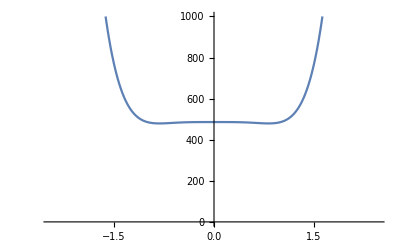

```mathematica
Plot[486-45 Subscript[μ, q]^4+45 Subscript[μ, q]^6,{Subscript[μ, q],-2.449489742783178,2.449489742783178},PlotRange->{0,1000}]
```

```mathematica
Reduce[d2>0]
```

μ_q∈Reals&&μ_q≠0

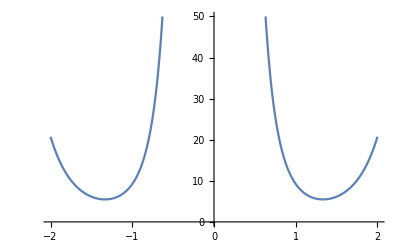

```mathematica
Plot[(√3 ⅇ^((5 Subscript[μ, q]^2)/6) (486+81 Subscript[μ, q]^2-45 Subscript[μ, q]^4+45 Subscript[μ, q]^6+25 Subscript[μ, q]^8))/(4 Subscript[μ, q]^4 (3+Subscript[μ, q]^2)^3),{Subscript[μ, q],-2,2},PlotRange->{0,50}]
```

```mathematica
Minimize[eff$sq1$minmax/.{Subscript[σ, k]->1},{Subscript[μ, q]}]//Simplify
```

{(25 √3 ⅇ^(1/4 (-1+√41)))/(8 (4+√41)),{μ_q→-√(3/10 (-1+√41))}}

```mathematica
Series[ⅇ^((5 Subscript[μ, q]^2)/6),{Subscript[μ, q],0,4}]
```

1+(5 μ_q^2)/6+(25 μ_q^4)/72+O[μ_q]^5

```mathematica
grad$eff$sq1$minmax=D[(eff$sq1$minmax/.{Subscript[σ, k]->1}), Subscript[μ, q]]//Simplify
```

(3 √3 ⅇ^((5 μ_q^2)/6) (-18+3 μ_q^2+5 μ_q^4))/(4 μ_q^3 (3+μ_q^2)^2)

```mathematica
sol=Solve[grad$eff$sq1$minmax==0&&Subscript[μ, q]>0,{Subscript[μ, q]}]
```

{{μ_q→√(1/10 (-3+3 √41))}}

```mathematica
eff$sq1$minmax/.{Subscript[σ, k]->1}/.sol//FullSimplify
```

{1/8 √3 (-4+√41) ⅇ^(1/4 (-1+√41))}

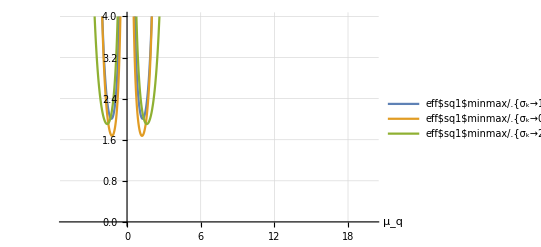

```mathematica
Plot[{eff$sq1$minmax/.{Subscript[σ, k]->1},
eff$sq1$minmax/.{Subscript[σ, k]->0.8},
eff$sq1$minmax/.{Subscript[σ, k]->2}
},{Subscript[μ, q],-5,20},GridLines->Automatic,PlotLegends->"Expressions",PlotRange->{0,4},AxesLabel->Automatic]
```

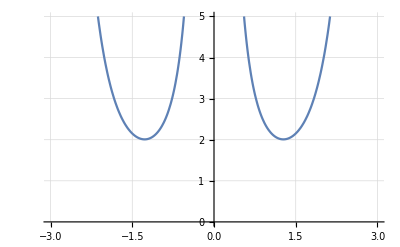

```mathematica
Plot[eff$sq1$minmax/.{Subscript[σ, k]->1},{Subscript[μ, q],-3,3},GridLines->Automatic,PlotRange->{0,5}]
```

```mathematica
Manipulate[Plot[eff$sq1$minmax/.{Subscript[μ, q]->mq1,Subscript[σ, k]->sk1},{sk1,0.0001,8},AxesLabel->Automatic],{mq1,0,8}]
```

```mathematica
Plot3D[eff$sq1$minmax,{Subscript[μ, q],0,3},{Subscript[σ, k],0.01,3},AxesLabel->Automatic,PlotRange->{0,1}]
```

-Graphics3D-

## Case 2: mean = 0, variance difference problem

```mathematica
eff$mq0=f$slope$fssd$mq0[v,Subscript[σ, q]^2,Subscript[σ, k]^2]/f$slope$lkstein$mq0[Subscript[σ, q]^2,κ^2]
```

(2 ⅇ^(v^2/(2+σ_k^2)-v^2/(σ_k^2+σ_q^2)) v^2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) σ_k^2 (2+σ_k^2)^3 (κ^2+2 σ_q^2)^3)/((κ^2)^(7/4) (-√(κ^2))^(3/2) (-4-κ^2)^(5/2) √(1+2/σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (-1+σ_q^2)^2 (σ_k^2+σ_q^2)^3)

```mathematica
eff$mq0/.{Subscript[σ, k]->1}//Simplify
```

(18 √3 ⅇ^(1/3 v^2 (1-3/(1+σ_q^2))) v^2 (12+20 κ^2+21 κ^4+8 κ^6+κ^8) (κ^2+2 σ_q^2)^3)/((12+v^2) (κ^2)^(7/4) (-√(κ^2))^(3/2) (-4-κ^2)^(5/2) (-1+σ_q^2)^2 (1+σ_q^2)^3)

```mathematica
(*Plot3D[f$eff$sq1[v,m],{v,-10,10},{m,-20,20}, PlotRange->{0,2},AxesLabel->{"v","mq"}]*)
```